```mathematica
Needs["utilities`"]
Get[FileNameJoin@{NotebookDirectory[],"generalizedKlyshkoCriteria.m"}]

probsList=Range[0,20];

Pinf=ConstantArray[0,Length@probsList];
Pvacuum=Pinf//ReplacePart[1->1];

generateMixedState[weights_,averages_,whichProbs_]:=Total[
(weights/Total@weights)Table[
poisson[λ,whichProbs],{λ,averages}
]
];

fockStateProbability[fock_Integer,whichProbs_]:=KroneckerDelta[#,fock]&/@whichProbs;

mixWith[originalProb_,newProb_,weight_]:=weight*originalProb+(1-weight)newProb;
repeatedMixtures[initialProb_,pairsOfProbs_List]:=Fold[
mixWith[#1,#2⟦2⟧,#2⟦1⟧]&,initialProb,pairsOfProbs
];
```

## Mix a bunch of coherent states and check criteria on them

```mathematica
componentsAverages={1,2,3};
componentsWeights={1,1,1}//#/Total@#&;
mixture=generateMixedState[componentsWeights,componentsAverages,probsList];
```

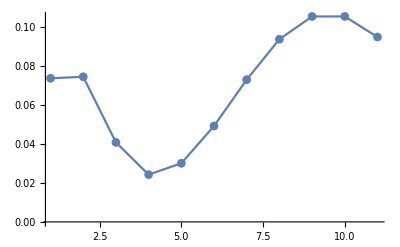

```mathematica
generateMixedState[{1,4},{1,9},Range[0,10]]//ListPlot[#,PlotRange->All,Joined->True,PlotMarkers->Automatic]&
```

Verify how the different Klyshko-like criteria are verified:

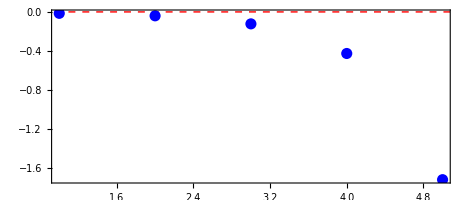

```mathematica
With[{criteriaIndices=Range[5]},
Graphics[
{
With[{val=klyshkoBasicCriteria[#,mixture]},
{If[val>0,Red,Blue],PointSize@0.02,
Point@{#,klyshkoBasicCriteria[#,mixture]}
}]&/@criteriaIndices,
{Red,Dashed,Thick,InfiniteLine@{{0,0},{1,0}}}
},
Frame->True
]]
```

Show also the K_∞ criteria

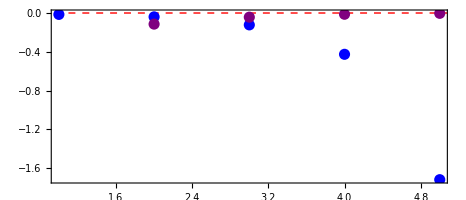

```mathematica
With[{criteriaIndices=Range[5]},
Graphics[
{
With[{val=klyshkoBasicCriteria[#,mixture]},{
If[val>0,Red,Blue],PointSize@0.02,
Point@{#,val}
}]&/@Range[5],
With[{val=klyshkoInfCriterion[#,mixture]},{
If[val>0,Green,Purple],PointSize@0.02,
Point@{#,val}
}]&/@{2,3,4,5},
{Red,Dashed,Thick,InfiniteLine@{{0,0},{1,0}}}
},
Frame->True
]]
```

```mathematica
Manipulate[
With[{mixedState=p mixture+(1-p)Pvacuum},
Graphics[{PointSize@0.02,
With[{val=klyshkoBasicCriteria[#,mixedState]},{
If[val>0,Red,Blue],
Point@{#,val}
}]&/@Range[4],
(*With[{val=klyshkoInfCriterion[#,mixedState]},{
If[val>0,Green,Purple],
Point@{#,val}
}]&/@{2,3,4,5},*)
Point@{0,(q[1]q[4]-q[0]q[5])/.q[n_]:>n!mixedState⟦n+1⟧},
{Red,Dashed,Thick,InfiniteLine@{{0,0},{1,0}}}
},Frame->True]],
{{p,1},0,2,0.01,Appearance->"Labeled"}
]
```

```mathematica
probsList=Range[0,20];

Pinf=ConstantArray[0,Length@probsList];
Pvacuum=Pinf//ReplacePart[1->1];

componentsAverages={1,3,8};
componentsWeights={1,2,5}//#/Total@#&;
mixture=Total[
componentsWeights*Table[
poisson[λ,probsList],{λ,componentsAverages}
]
];
```

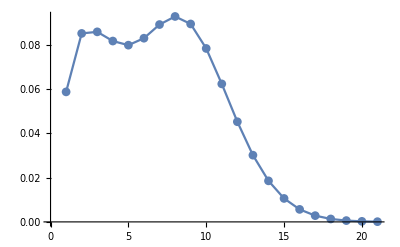

```mathematica
ListPlot[mixture,Joined->True,PlotMarkers->Automatic]
```

```mathematica
Manipulate[
With[{mixedState=repeatedMixtures[mixture,{
{p3,fockStateProbability[3,probsList]},
{p2,fockStateProbability[2,probsList]},
{p1,fockStateProbability[1,probsList]},
{p0,fockStateProbability[0,probsList]},
{pInf,Pinf}
}]},
Column[{
Graphics[{PointSize@0.02,
With[{listOfPairs=(Table[q[n]/q[n+1],{n,0,4}]/.{q[n_]:>n! mixedState⟦n+1⟧})},
Table[{
If[listOfPairs⟦idx⟧≥listOfPairs⟦idx+1⟧,Green,Red],
Point@{idx,listOfPairs⟦idx⟧}
},
{idx,Range[Length@listOfPairs-1]}]
],
Point@{-1,200klyshkoInfCriterion[4,mixedState]},
{Red,Dashed,Thick,InfiniteLine@{{0,0},{1,0}}}
},Frame->True,ImageSize->400,AspectRatio->1/GoldenRatio],
ListPlot[{
mixedState,
poisson[mixedState⟦2⟧/mixedState⟦1⟧,Range[0,Length@mixedState-1]]
},
ImageSize->400,Joined->True,PlotMarkers->Automatic]
}]],
{{p3,1},0,2,0.0001,Appearance->"Labeled"},
{{p2,1},0,2,0.0001,Appearance->"Labeled"},
{{p1,1},0,2,0.0001,Appearance->"Labeled"},
{{p0,1},0,2,0.0001,Appearance->"Labeled"},
{{pInf,1},0,1.2,0.0001,Appearance->"Labeled"},ControlPlacement->Right
]
```

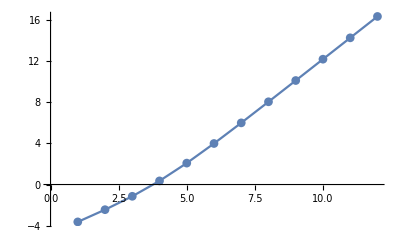

```mathematica
With[{foo=mixture⟦;;13⟧},
ListPlot[
Log@Differences[foo*Range[0,Length@foo-1]!],
Joined->True,PlotMarkers->Automatic]]
```

The optimal procedure seems to progressively mix with P_(n-1),P_(n-2),...,P_1, and then finally P_∞. Let’s see if it works algorithmically

Let’s focus on (P_0,P_1,P_2,P_3) for starters

```mathematica
klyshkoBasicCriteria[2]
```

4 P[2]^2-6 P[1] P[3]

```mathematica
fockStateProbability[2,probsList]
```

{0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
statesFirstStep=With[{mixedWithP2=mixWith[mixture,fockStateProbability[2,probsList],p]⟦;;4⟧},
klyshkoBasicCriteria[2,mixedWithP2]//N//mixedWithP2/.Echo@Solve[#==0,p]&
]
```

{{p→0.979331},{p→1.89948}}

{{0.180524,0.257209,0.242211,0.152058},{0.350138,0.498874,-0.469784,0.294927}}

```mathematica
klyshkoBasicCriteria[1,#]&/@statesFirstStep
```

{-0.0212934,0.577854}

## Try to estimate the volume of the classical set

```mathematica
numSamples=100000;
randomProbs4D=Select[RandomReal[{0,1},{24numSamples,4}],Total@#≤1&];
```

```mathematica
Length@Select[randomProbs4D,
And[
klyshkoInfCriterion[3,#]≤0,
klyshkoBasicCriteria[1,#]≤0,
klyshkoBasicCriteria[2,#]≤0
]&
]/Length@randomProbs4D//N
```

0.0223993

```mathematica
Q[n-2]/Q[n-1]==Q[n-1]/Q[n]/.Q[k_]:>k! P[k]/.P[k_]:>ϵ P[k]+(1-ϵ)KroneckerDelta[k,n]//Solve[#,ϵ]&//Simplify
```

{{ϵ→(-(-2+n)! n! P[-2+n]+√((-2+n)!) √(n!) √((-2+n)! n! P[-2+n]^2))/(-2 ((-1+n)!)^2 P[-1+n]^2+2 (-2+n)! n! P[-2+n] (-1+P[n]))},{ϵ→-((-2+n)! n! P[-2+n]+√((-2+n)!) √(n!) √((-2+n)! n! P[-2+n]^2))/(-2 ((-1+n)!)^2 P[-1+n]^2+2 (-2+n)! n! P[-2+n] (-1+P[n]))}}

```mathematica
Q[n-2]Q[n]-Q[n-1]Q[n-1]/.Q[k_]:>k! P[k]/.P[k_]:>ϵ P[k]+(1-ϵ)KroneckerDelta[k,n-1]//Collect[#,ϵ,Simplify]&
```

-((-1+n)!)^2-2 ϵ ((-1+n)!)^2 (-1+P[-1+n])+ϵ^2 (-((-1+n)!)^2+2 ((-1+n)!)^2 P[-1+n]-((-1+n)!)^2 P[-1+n]^2+(-2+n)! n! P[-2+n] P[n])

```mathematica
Q[n-2]Q[n]-Q[n-1]Q[n-1]/.Q[k_]:>k! P[k]/.P[k_]:>ϵ P[k]+(1-ϵ)KroneckerDelta[k,n-1]//Solve[#==0,ϵ]&//Simplify
```

{{ϵ→(((-1+n)!)^2-((-1+n)!)^2 P[-1+n]-√((-2+n)!) √(n!) √(((-1+n)!)^2 P[-2+n] P[n]))/(((-1+n)!)^2-2 ((-1+n)!)^2 P[-1+n]+((-1+n)!)^2 P[-1+n]^2-(-2+n)! n! P[-2+n] P[n])},{ϵ→(((-1+n)!)^2-((-1+n)!)^2 P[-1+n]+√((-2+n)!) √(n!) √(((-1+n)!)^2 P[-2+n] P[n]))/(((-1+n)!)^2-2 ((-1+n)!)^2 P[-1+n]+((-1+n)!)^2 P[-1+n]^2-(-2+n)! n! P[-2+n] P[n])}}

```mathematica
%/.n->3
```

{{ϵ→(4-4 P[2]-2 √6 √(P[1] P[3]))/(4-8 P[2]+4 P[2]^2-6 P[1] P[3])},{ϵ→(4-4 P[2]+2 √6 √(P[1] P[3]))/(4-8 P[2]+4 P[2]^2-6 P[1] P[3])}}